All-Optical Radiation Reaction at 10^21 W/cm^2

M. Vranic, J. L. Martins, J. Vieira, R. A. Fonseca, and L. O. Silva, Phys Rev Lett 113, 134801 (2014)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce figure 3.

## Figure 3: Electron beam energy loss

(In the units chosen in the paper, the classical electron radius, present in the Thompson cross section, is re=  e^2/(m c^2) while in SI re=1/(4π ϵ0)  e^2/(m c^2))

3.43767×10^-25 Ι

3.392×10^-25 Ι

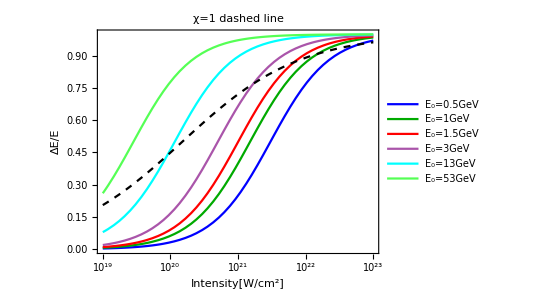

```mathematica
(* LP PW laser colliding against a relativistic electron *)
Clear[γ,γf,γ0,k,k3,η,EGeV,τ0,τ0fs,e,m,c,λ,a0,ω0,ΔEE,χ,ΔEEχ,ϵ0]

(* equation 3 *)
γf=γ0/(1+k γ0);(*[] final electron energy *)
k3=1/(4π ϵ0)(1-Cos[π])^2 η/3(e^2 ω0^2)/(m c^3)a0^2 τ0;(*[] CRR k factor from equation 3 *)
k=(1-Cos[π])^2 3.2 10^-5(Ι 10^-22)τ0fs;(*[] CRR k factor Engineering formula *)
ΔEE=(γ0-γf)/γ0;(*[] 0<=energy loss<=1 *)

(* χ=1: χ~2 γ0 a0/aS *)
(*Solve[γf==γ0/(1+k γ0),γ0][[1,1,2]]*)
γ=Solve[1==2γ a0/(411823),γ][[1,1,2]];
ΔEEχ=ΔEE//.{γ0->γ};

(* physical constants *)
e=1.6 10^-19;(*[C]*)
m=9.1 10^-31;(*[Kg]*)
c=3 10^8;(*[m/s]*)
ϵ0=8.854 10^-12;(*[F/m] vacuum permittivity*)

(* parameters *)
η=0.4;(*[] temporal profiles *)
τ0=26.5 10^-15;(*[s]*)
τ0fs=τ0 10^15;(*[fs]*)
λ=1;(*[μm] laser central wavelength *)
ω0=2π c/(λ 10^-6)//N;(*[1/s] laser frequency *)
a0=0.855 Sqrt[Ι 10^-18]λ;(*[] laser a0 *)
γ0=EGeV/(0.511 10^-3);(*[] electron γ from GeV to boost *)

(* compare the CRR k factors of equation 3 and the "engineering formula" *)
k3
k
(*k ~ 4.64 10^-7 a0^2 for these parameters *)

(* plot *)
LogLinearPlot[{ΔEE/.{EGeV->0.5},ΔEE/.{EGeV->1},ΔEE/.{EGeV->1.5},ΔEE/.{EGeV->3},ΔEE/.{EGeV->13},ΔEE/.{EGeV->53},ΔEEχ},{Ι,10^19,10^23},Frame->True,FrameLabel->{"Intensity[W/cm^2]","ΔE/E"},PlotRange->{0,1},PlotStyle->{Blue,Darker[Green],Red,Lighter[Purple],Cyan,Lighter[Green],{Dashed,Black}},PlotLegends->{"E_0=0.5GeV","E_0=1GeV","E_0=1.5GeV","E_0=3GeV","E_0=13GeV","E_0=53GeV"},AspectRatio->3/4,PlotLabel->"χ=1 dashed line"]
```

## η factor for the two envelopes (+Gaussian)

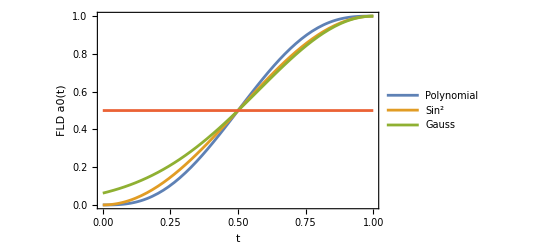

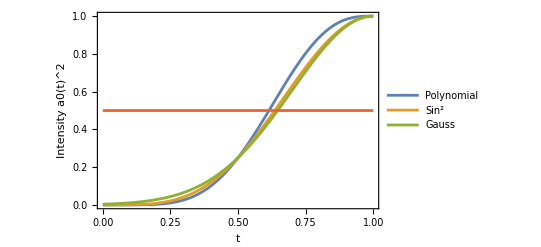

poly: 181/462=0.391775

sin2: 3/8=0.375

gauss: 1/4 √(π/Log[4])=0.376346

0.957182

0.956633

```mathematica
Clear[t,τ,τ0,aPoly,aSin2,aGauss,intPoly,intSin2,intGauss]
τ0=1;(*[] normalize all times to τ0 *)
τ= t/τ0;

aPoly=10 τ^3-15 τ^4+6 τ^5;(* polynomial envelope. instead of using τ=√2 t/τ0 as in the paper (which would give incorrect integrals) we use simply τ=t/τ0 to be able to compare between the two envelopes  *)
aSin2=Sin[(π t)/(2τ0)]^2;(* sin^2 envelope *)
aGauss=Exp[-4Log[2](1-t/τ0)^2];(* sin^2 envelope *)

(* plot the three envelopes with same fwhm in field, not intensity *)
Plot[{aPoly,aSin2,aGaus,0.5},{t,0,τ0},Frame->True,FrameLabel->{"t","FLD a0(t)"},PlotLegends->{"Polynomial","Sin^2","Gauss"}]
(* plot also intensity *)
Plot[{aPoly^2,aSin2^2,aGaus^2,0.5},{t,0,τ0},Frame->True,FrameLabel->{"t","Intensity a0(t)^2"},PlotLegends->{"Polynomial","Sin^2","Gauss"}]

(* the k factor will be proportional to a(t)^2. since the envelopes are symmetric, we only integrate up to t=τ0 *)
intPoly=Integrate[aPoly^2,{t,0,τ0}];
Print["poly: ", intPoly, "=",intPoly//N]
intSin2=Integrate[aSin2^2,{t,0,τ0}];
Print["sin2: ", intSin2, "=",intSin2//N]
intGauss=Integrate[aGauss^2,{t,-∞,τ0}];
Print["gauss: ", intGauss, "=",intGauss//N]

(* the ratio of the integrals from this notebook *)
intSin2/intPoly//N
(* the ratio of the integrals from the paper *)
0.375/0.392
```